# Quantum Wells -- Eigenvalues of the Schrödinger Equation

## Introduction

We investigate the bound states of a particle in a quantum well in one dimension with potential V(x), where V(x) ≤ 0 and V(x) → 0 for |x| → ∞.  This notebook shows one way to do this using Mathematica.  In units where ℏ = m = 1 (where m is the mass of the particle), Schrödinger's equation is

(d^2 ψ)/(d x^2) + 2 (E - V(x)) ψ = 0

We take the potential to be an even function of x, so the wave functions are either even or odd functions of x, ψ(x) = ±ψ(-x). The sign, +1 or -1, is called the parity of the state. It is shown in the textbooks on quantum mechanics  that (i)  the ground state is symmetric ψ(x) = ψ(-x) and has no zeroes (nodes), (ii) the first excited state is odd and has one node, and (iii) for each higher energy eigenvalue the the number of nodes increases by one and the parity alternates. 

We will find the lowest energy level and corresponding wavefunction for each parity. We will set up a numerical method, but, in this notebook, only apply it to a simple case where the solution can also be obtained exactly, namely the rectangular well of width L and depth V_0(< 0), i.e. where V(x) = 0 for |x| > L/2 and V(x) =  V_0 for |x| ≤ L/2. We take L = 1, and initially take V_0= -8. 

First, therefore, we set up the potential and plot it.

```mathematica
Clear["Global`*"]
```

```mathematica
L = 1;
```

```mathematica
v0 = -8;
```

```mathematica
v[x_] := v0 /; Abs[x] <= L/2
```

```mathematica
v[x_] := 0 /; Abs[x] > L/2
```

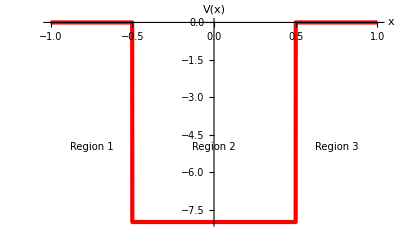

```mathematica
Plot[v[x], {x, -L, L} ,PlotStyle -> {Red, AbsoluteThickness[3]},AxesStyle -> AbsoluteThickness[1],  AxesLabel -> {"x", "V(x)"}, Epilog -> {Text[Style["Region 1", FontSize -> 10], {-0.75, -5}] , Text[Style["Region 3",FontSize -> 10], {0.75, -5}],  Text[Style["Region 2", FontSize -> 10], {0, -5}]}]
```

Although we only consider the rectangular well here, the numerical method can be applied to any potential which is an even function of x vanishes outside some range of x (at least to a sufficiently good approximation) simply by changing the expression for V(x).

## Setting up the Problem

In region 1,  ψ_1= A e^κxwhere κ = √(2|E|),and in region 3, ψ_3= B e^-κx, so we set up these functions:

```mathematica
B = 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
```

```mathematica
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

The variable en is the energy.
We also define the Schrödinger equation for region 2, using a delayed assignment, ":=", since we will only use it later:

```mathematica
eqn[en_] := ψ2''[x] + 2(en - v[x])ψ2[x]
```

We also set up the calculation of the wavefunction in region 2 matching the function and its derivative to ψ_1at x=-L/2. We will adjust the energy so that either the derivative of ψ vanishes at x=0 (for even eigenfunctions) or ψ vanishes (for odd eigenfunctions). This value for the energy will be an eigenvalue. Since the energy will be determined by a boundary condition at x = 0 we only need to integrate from x = -L/2 up to x = 0.

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

Note that it is necessary to set the energy variable en, used in the computation of ψ_1 and ψ_3, to the current value of the variable energy  used in the function wavefunc2. This is done first and then NDSolve  is called to solve the Schrödinger equation. We define wavefunc2[en_] with a delayed assignment, so that each time it is called, the differential equation is integrated again. This is what we want in order to calculate the eigenvalue.  Note that wavefunc2[en_] will be given as a replacement rule in the form {{ψ2→InterpolatingFunction[{{-0.5,0.5}},"<>"]}}. However, it is more convenient to obtain the wavefunction in region 2 directly as a function of x.  To do so we define sol2[x, en] by

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

which applies the replacement rule and removes the outer set of curly brackets by taking the first element of the list. Note too that we have added the hieroglyphics
	?NumericQ
to the arguments of sol2. This is necessary in Mathematica version 5 and later when the solution is put into FindRoot below to determine the energy eigenvalue.(?NumericQ imposes that the function is only evaluated if the arguments are numerical.)  It is also convenient to define a function for the derivative of the wave function (since we will require that this is zero at x=0 for the even parity solutions):

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

## Even Parity Solution

We are now in a position to start calculating. First of all we look for an even eigenfuction by  setting B = A and requiring that the derivative of the wavefunction vanishes at x = 0. We give two initial starting guesses for the eigenvalue, -5  and -8.

```mathematica
A = B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -5, -8} ]
```

-5.87875

We conclude that  E =-5.87875 is an eigenvalue corresponding to an even eigenfunction of the Hamiltonian. For this simple example of the rectangular well we can explicitly verify that it is an eigenvalue by working out the exact solution. As the  textbooks show,  even-parity  eigenvalues are given by the solutions of

κ = k tan(kL/2)

where k =  √(2(|V_0| - |E|)). We also solve this equation with FindRoot, starting with the numerical value found above, eval, as the initial guess:

```mathematica
kappa :=Sqrt[ Abs[2analen] ]; k := Sqrt[2 (Abs[v0]  - Abs[analen])];
 evalanal =analen /.FindRoot [ kappa ==  k Tan [k L / 2] , {analen, eval} ]
```

-5.87875

The numbers for eval and evalanal agree showning that our numerical method correctly found an even-parity eigenvalue.

Now we want the eigenfunction coresponding to our eigenvalue. Since we know the eigenvalue, we do not  want to keep recalculating  the wavefunction so we define a function efunc2 with immediate assignment, and input the eigenvalue for the energy

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

(where[[1]] removes one set of curly bracket as above). (Calling wavefunct2 not only computes the eigenfunction in Region 2, but also sets the value of the energy to be used in ψ1 and ψ3 to the desired eigenvalue.) We have now obtained the eigenfunction in all three regions, so let's collect these into a single (not normalized) function ψnn[x_], which can then easily be plotted (remember that we only computed  efunc2[x] for -L/2 ≤ x < 0, and so we also have to specify it for 0 ≤  x ≤ L/2, noting that the eigenfunction is even):

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

Note the use of the symbol /; , which means "provided that".

We first normalize the wavefunction, using immediate assignment so that the normalization constant is not recomputed each time a value for the normalized wave function is needed for the plot.

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

and then plot it. We first define the plot for ψnorm (but do not yet display it because of the semicolon after the command). Then we add the labels with the Show[Graphics[... ]] command. This looks a bit complicated but has the advantage that the current values of the well depth and width, and the eigenvalue are automatically printed without needing to modify this command each time.

```mathematica
fig = Plot[ψ[x], {x, -1.2L, 1.2L}, PlotStyle -> {AbsoluteThickness[2], Red},AxesLabel -> {"x", "ψ"} ];
```

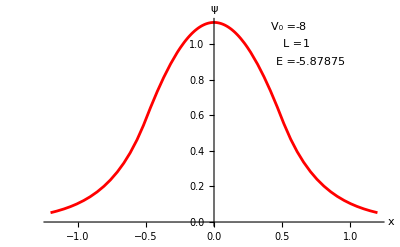

```mathematica
Show[fig,  Graphics [ { 
			Text[ en , {0.6, 0.9}, {-1, 0} ] ,
Text[ "E = ", {0.6, 0.9}, {1, 0}  ],
			Text[  v0, {0.6, 1.1}, {-1, 0} ] ,
Text[ "V_0 = ", {0.6, 1.1}, {1, 0}  ],
			Text[ "L = ", {0.65, 1}, {1, 0}], Text[ L, {0.65, 1}, {-1, 0}]  } ] ]
```

We see that the wavefunction matches up smoothly at x = ±L/2 (i.e. ±1/2) as expected. Also there are no nodes (zeroes) in the wavefunction which means, since we are in one dimension, that it is the ground state.

## Odd Parity Solution

Now we look at odd-parity solutions.by requiring

```mathematica
A = -B;
```

and looking for a solution where ψ vanishes at x = 0. We give two starting estimates for the eigenvalue of -0.5 and -2.

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -0.5, -2} ]
```

-0.814203

We check that the eigenvalue agrees with the analytical eigenvalue, which is a solution of κ = –k cot (kL / 2).

```mathematica
evalanal = analen /.FindRoot [ kappa == - k Cot [k L / 2] , {analen, eval} ]
```

-0.814203

Indeed it agrees.

Next we calculate the eigenfunction for -L/2 ≤ x ≤ 0 using immediate assignment and the energy set to the eigenvalue.

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

We also need to redefine eigenfunction for 0 ≤ x ≤ L/2 (where we didn't explicitly compute it) since it is now odd (not even)

```mathematica
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2
```

and to compute the normalization factor for this state

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

Everything else is the same as for the even-parity eigenstate and uses a delayed assignment. Hence we can now create the figure for the normalized wavefunction

```mathematica
fig = Plot[ψ[x], {x, -2L,2L}, PlotStyle -> {AbsoluteThickness[2], Red},AxesLabel -> {"x", "ψ"} ];
```

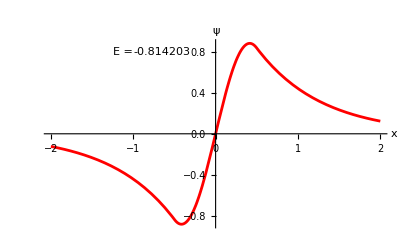

```mathematica
Show[fig,  Graphics [ { 
			Text[ en , {-1, 0.8}, {-1, 0} ] ,
Text[ "E = ", {-1, 0.8}, {1, 0}  ],
			Text[  v0, {-0.6, 1.2}, {-1, 0} ] ,
Text[ "V_0 = ", {-0.6, 1.2}, {1, 0}  ],
			Text[ "L = ", {-0.57, 1}, {1, 0}] , 	Text[ L, {-0.57, 1}, {-1, 0}]} ] ]
```

Again the wavefunction and its derivative are continuous at the walls of the well, i.e. at x = ± 1/2. The wavefunction has only one node, showing that it is indeed the lowest energy odd-parity eigenstate.

## Conclusions

The method can now be used to determine eigenvalues and eigenvectors  for other potential wells where analytical solutions don't exist provided V(x) = 0 for |x| > L/2.  Two examples which you could consider are:

(a)  A single well

V(x) = - V_0/2 [1 + cos (2π x / L ) ],   (-L/2 < x < L/2)

and V(x) = 0, otherwise. This has depth -V_0 at x = 0 and vanishes as |x| → L/2.

(b) A double well

V(x) = - V_0/2 [1 - cos (4π x / L ) ],   (-L/2 < x < L/2)

which vanishes at x = 0 and ± L/2, and has minima of depth -V_0 at x = ± L/4. Increase the depth of the potential and notice how the lowest even and odd energies become close to each other. Explain this in terms of quantum mechanical tunneling. 

You can also obtain higher energy bound states of either parity by giving different starting values to the FindRoot command. For a given value of the well depth it is of interest to determine how many bound states there are. You will find that there is always one bound state (this is a feature of one-dimension; it is not true in three dimensions) and this is of even parity and has no nodes. However, the well needs to be sufficiently deep for a second bound state to appear.

The method used here relies on the potential vanishing for |x| > L/2. More general potential wells can be studied using a similar but somewhat more complicated method called the "shooting method", see e.g.  my handout on this, and Kinzel, Physics by Computer, p. 130-135.